```mathematica
path="C:\\SC Lab\\GitHubRepositories\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
```

# Fig 2

```mathematica
file=path<>"circles_data_1227.hdf5";
(*file=path<>"sup_circles_data.hdf5";*)
data=Import[file, "Data"];
power = data["/power"]
freq = data["/freq"];
refl=data["/R_real"]+I data["/R_imag"];
```

{-10.,-5.,0.,5.,10.}

```mathematica
powerRef=0;
npower=Length[power];
nfreq=Length[freq];
MinFreq=Min[freq];
MaxFreq=Max[freq];
MinPowerInd=1;
MaxPowerInd=npower;
tofit=Table[{freq[[j]],10^((power[[k]]-powerRef)/10),l,l*Im@refl[[j,k]]+(1-l)*Re@refl[[j,k]]},{k,MinPowerInd,MaxPowerInd},{l,0,1},{j,1,nfreq}];
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{f0→6.54453,Γ→0.00174248,p→0.782267,α→5.56783×10^-7}

{0.235962,0.419607,0.746179,1.32691,2.35962}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::munfl: 0.00203529^943. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | Confidence Interval
f0 | 6.54453 | 3.40393×10^-6 | {6.54452,6.54453}
Γ | 0.00174248 | 0.0000102325 | {0.00172241,0.00176255}
p | 0.782267 | 0.0036187 | {0.77517,0.789364}
α | 5.56783×10^-7 | 1.0706×10^-8 | {5.35786×10^-7,5.7778×10^-7}

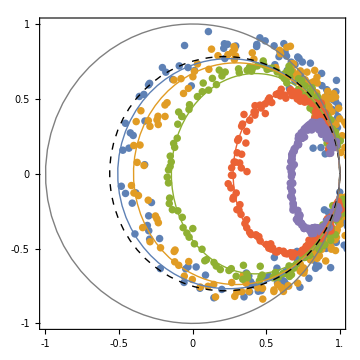

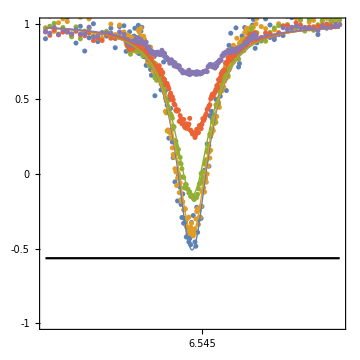

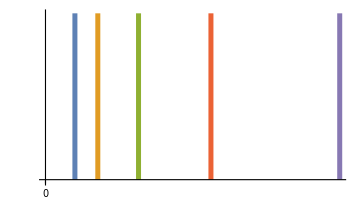

```mathematica
fit=FindFit[Flatten[tofit,2],(1-s)*Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α   P)]+s*Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α P)],{{f0,(freq[[1]]+freq[[-1]])/2},{Γ,1.82*^-3},{p,0.757},{α,0.003}},{f,P,s}]
PlotIndices={1,2,3,4,5};
ΩRabi =10^3 √(α 10^((power[[MinPowerInd;;MaxPowerInd]]-powerRef)/10))/.fit

initguessS={{f0,(freq[[1]]+freq[[-1]])/2},{Γ,1.82*^-3},{p,0.757},{α,0.003}};
(*BoundS={A==FixedLowerBound-FixedUpperBound,B==FixedUpperBound,TR>0};*)
model=(1-s)*(1-(2 p Γ (Γ))/(4 (f-f0)^2+Γ^2+2α  P))+s*(-(2 p Γ (2  (f-f0)))/(4 (f-f0)^2+Γ^2+2α P));
model=(1-s)*Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α   P)]+s*Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α P)];
nmf=NonlinearModelFit[Flatten[tofit,2],model,initguessS,{f,P,s}];
sparam=nmf["BestFitParameters"];
nmf["ParameterConfidenceIntervalTable"]


g1=Show[ListPlot[Table[Transpose@{tofit[[i,1,;;,-1]],tofit[[i,2,;;,-1]]},{i,PlotIndices}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1,PlotStyle->PointSize[0.015]],
ParametricPlot[Evaluate@Table[{Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])],Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])]}/.fit,{i,PlotIndices}],{f,5,8},PlotPoints->1000,PlotRange->All,PlotStyle->Thick],
ParametricPlot[Evaluate@{Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)],Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)]}/.fit,{f,5,8},PlotPoints->1000,PlotRange->All,PlotStyle->Directive[Black,Thick,Dashed]],
ParametricPlot[Evaluate@{Re[1-(2 Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)],Im[1-(2  Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)]}/.fit,{f,5,8},PlotPoints->1000,PlotRange->All,PlotStyle->Directive[Gray,Thick]]
,Frame->True,FrameTicks->{{{-1,-0.5,0,0.5,1},None},{{-1,-0.5,0,0.5,1.0},None}},FrameTicksStyle->Directive[Black,16],ImageSize->Medium]

g2=Show[ListPlot[Table[Transpose@{tofit[[i,1,;;,-4]],tofit[[i,1,;;,-1]]},{i,PlotIndices}],PlotStyle->PointSize[0.01],PlotRange->{{MinFreq,MaxFreq},{-1,1}}],Plot[Evaluate@Table[Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])]/.fit,{i,PlotIndices}],{f,MinFreq,MaxFreq},PlotRange->All,PlotStyle->Thick],
Plot[1-2p/.fit,{f,MinFreq,MaxFreq},PlotStyle->Black],Frame->True,FrameTicks->{{{-1,-0.5,0,0.5,1},None},{Table[6.53+0.005i,{i,0,10}],None}},FrameTicksStyle->Directive[Black,16],AspectRatio->1,ImageSize->Medium]


g3=ParametricPlot[Evaluate[{#,x}&/@ΩRabi],{x,-0,0.5},PlotStyle->Thickness[0.01],Ticks->{Table[i,{i,0,10}],None},TicksStyle->Directive[Black,"Arial", 14]]
```

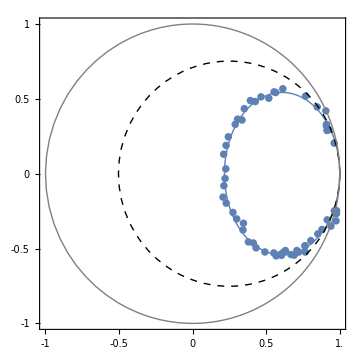

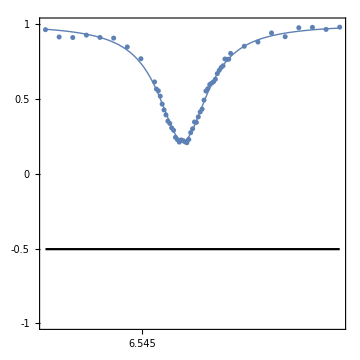

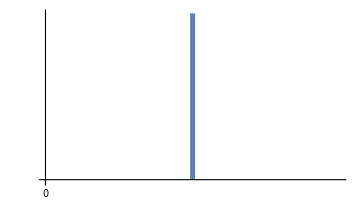

```mathematica
.
```

```mathematica
Export[path<>"circles.eps",g1]
Export[path<>"circles_real_part.eps",g2]
Export[path<>"Omega_rabi.eps",g3]
```

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\circles.eps

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\circles_real_part.eps

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\Omega_rabi.eps

# Fig 3

```mathematica
FixedUpperBound=Mean[{0.7133940085771162,0.4866773887549828+0.275317557041368}];
FixedLowerBound=Mean[{0.7133940085771162-0.4876694481415331,0.4866773887549828-0.275317557041368}];
```

```mathematica
PtSize=0.035;
```

## Rabi

{A→0.259576,B→0.478118,Ω→0.00596182,TR→168788.}

83.867

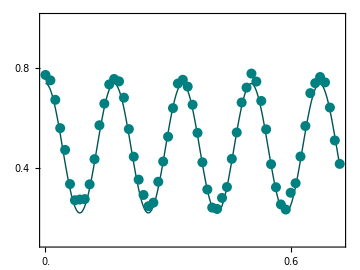

```mathematica
file = path <> "rabi_data.hdf5";
data = Import[file, "Data"];
delays = data["/x"];
population = data["/y"];

fit = FindFit[
  Transpose[{delays, 
    population}], {A*Cos[2 π*Ω*t]*
     Exp[-t/TR] + B, {A == (FixedUpperBound - FixedLowerBound)/2, 
    B == (FixedUpperBound + FixedLowerBound)/2}}, {{A, 0.3}, 
   B, {Ω, 0.004},{TR, 1000}}, t]
Pratio01 = (B2 - A2)/(B2 + A2);
P0ini = 0.5;
r0 = 0.5;
1/(Ω)/2/.fit
g = Show[Plot[(A*Cos[2 π*Ω*1000*t]*
        Exp[-(1000 t)/TR] + B)*(P0ini/r0) /. fit, {t, 0, 
    delays[[-1]]/1000}, 
   PlotStyle -> Directive[Darker@RGBColor[0, 0.5, 0.5], Thick], 
   PlotRange -> {0.1, 1}], 
  ListPlot[Transpose@{delays/1000, population*(P0ini/r0)}, 
   PlotStyle -> {PointSize[PtSize], RGBColor[0, 0.5, 0.5]}], 
  FrameTicks -> {{Table[0.2 i, {i, 0, 10}], 
     None}, {Table[0.2 i, {i, 0, 10}], None}}, Frame -> True, 
  FrameTicksStyle -> Directive[Black, 16], ImageSize -> Medium, 
  AspectRatio -> 0.75]
```

```mathematica
Export[path<>"rabi.eps",g]
```

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\rabi.eps

```mathematica
rTop=0.259576+0.478118;
rBot=-0.259576+0.478118;
rBot/rTop
```

0.29625

```mathematica
1/(0.29625+0.007+1)
```

0.767312

```mathematica
84./Sqrt[2π]
```

33.5112

```mathematica
rTop=0.267+0.474;
rBot=-0.267+0.474;
rBot/rTop
1/(0.279352+0.007+1)
```

0.279352

0.777392

## T1

```mathematica
file=path<>"t1_ramsey_echo_data.hdf5";
data=Import[file, "Data"];
delays = data["/x"];
population = data["/y"];
T1Population=population[[1]];
T2RamseyPopulation=population[[2]];
T2Population=population[[3]];
```

FittedModel::constr: The property values {ParameterConfidenceIntervalTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
A | -0.519152 | 0.0116581 | {-0.542996,-0.495309}
B | 0.737694 | 0.00735354 | {0.722655,0.752734}
TR | 51719. | 2634.53 | {46330.8,57107.2}

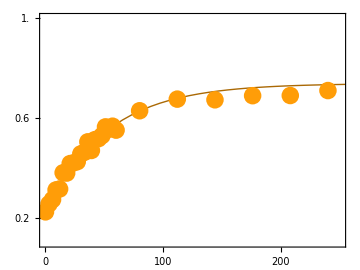

```mathematica
scale=P0ini/r0;
initguessS={{A,0.5},{B,0.8},{TR,50000}};
BoundS={A==FixedLowerBound-FixedUpperBound,B==FixedUpperBound,TR>0};
model=A*Exp[-t/TR]+B;
data=Transpose[{delays,T1Population*scale}];
nmf=NonlinearModelFit[data,{model,BoundS},initguessS,t];
sparam=nmf["BestFitParameters"];
nmf["ParameterConfidenceIntervalTable"]
dataS=Transpose[{delays/1000,T1Population*scale}];
g=Show[Plot[((nmf[t*1000]/.sparam)),{t,0,delays[[-1]]/1000},PlotStyle->Directive[Darker@RGBColor["#FF9D08"],Thick],PlotRange->{{0,250},{0.1,1}}],ListPlot[dataS,PlotStyle->Directive[PointSize[PtSize],RGBColor["#FF9D08"]]],FrameTicks->{{Table[0.2i,{i,-5,5}],None},{Table[50i,{i,0,7}],None}}, Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
nmfT1=nmf;
sparamT1=sparam;
dataT1=dataS;
```

```mathematica
Export[path<>"t1.eps",g]
```

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\t1.eps

## T2

FittedModel::constr: The property values {ParameterConfidenceIntervalTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
A | 0.259576 | 0.00922524 | {0.240708,0.278444}
B | 0.478118 | 0.00582737 | {0.4662,0.490037}
TR | 51859.9 | 4185.76 | {43299.,60420.7}

FittedModel::constr: The property values {ParameterConfidenceIntervalTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
A | -0.259576 | 0.0137878 | {-0.287866,-0.231286}
B | 0.478118 | 0.00316669 | {0.471621,0.484616}
TR | 26303.5 | 2357.35 | {21466.7,31140.4}
Ω | 0.0000297344 | 6.42547×10^-7 | {0.000028416,0.0000310527}
ϕo | 0.0709616 | 0.0740053 | {-0.0808848,0.222808}

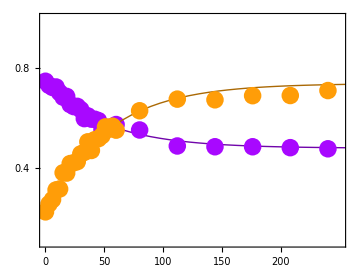

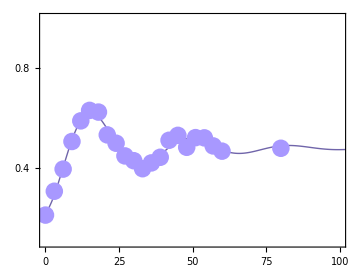

```mathematica
data=Transpose[{delays,T2Population*scale}];
BoundS={A==(-FixedLowerBound+FixedUpperBound)/2,B==(FixedUpperBound+FixedLowerBound)/2,TR>0};
initguessS={{A,0.5},{B,0.8},{TR,50000}};
model=A*Exp[-t/TR]+B;
nmf=NonlinearModelFit[data,{model,BoundS},initguessS,t];
sparam=nmf["BestFitParameters"];
nmf["ParameterConfidenceIntervalTable"]
dataS=Transpose[{delays/1000,T2Population*scale}];
dataRamsey=Transpose[{delays,T2RamseyPopulation*scale}];
BoundS={A==-(-FixedLowerBound+FixedUpperBound)/2,B==(FixedUpperBound+FixedLowerBound)/2,TR>0,0.001>Ω>0};
modelRamsey=A*Cos[2π*Ω*t+ϕo]*Exp[-t/TR]+B;
initguessS={{A,0.5},{B,0.8},{TR,50000},{Ω,0.00002973452815432999},{ϕo,0}};
nmfRamsey=NonlinearModelFit[dataRamsey,{modelRamsey,BoundS},initguessS,t];
sparamRamsey=nmfRamsey["BestFitParameters"];
nmfRamsey["ParameterConfidenceIntervalTable"]
dataSRamsey=Transpose[{delays/1000,T2RamseyPopulation*scale}];
g=Show[Plot[(nmf[t*1000]/.sparam),{t,delays[[1]]/1000,delays[[-1]]/1000},PlotStyle->Directive[Darker@RGBColor["#A808FF"],Thick],PlotRange->{{0,250},{0.1,1}}],ListPlot[dataS,PlotStyle->Directive[RGBColor["#A808FF"],PointSize[PtSize]]], Plot[(nmfT1[t*1000]/.sparamT1),{t,delays[[1]]/1000,delays[[-1]]/1000},PlotStyle->Directive[Darker@RGBColor["#FF9D08"],Thick],PlotRange->{{0,250},{0.1,1}}],ListPlot[dataT1,PlotStyle->Directive[RGBColor["#FF9D08"],PointSize[PtSize]]],Frame->True,FrameTicks->{{Table[0.2i,{i,0,8}],None},{Table[50i,{i,0,4}],None}}, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
g=Show[Plot[(nmfRamsey[t*1000]/.sparamRamsey),{t,delays[[1]]/1000,delays[[-1]]/1000},PlotStyle->Directive[Darker@RGBColor["#A898FF"],Thick],PlotRange->{{0,100},{0.1,1}}],ListPlot[dataSRamsey,PlotStyle->Directive[RGBColor["#A898FF"],PointSize[PtSize]]],Frame->True,FrameTicks->{{Table[0.2i,{i,0,8}],None},{Table[25i,{i,0,4}],None}}, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
```

```mathematica
Export[path<>"t2.eps",g]
```

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\t2.eps

# Fig 4

```mathematica
path="C:\\SC Lab\\GitHubRepositories\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
Needs["ErrorBarPlots`"]
file=path<>"transient_data_final.hdf5";
data=Import[file, "Data"];
(*delays = Join[data["/time0"],data["/time"]];*)
delays = data["/time"];
power=data["/power"]
population=data["/y"];
(*population= Join[data["/y0"],data["/y"]]*)
initguessS={{A,0.2},{B,0.4},{TR,20000}};
BoundS={1>A>-1,1>B>0,TR>0};
model=A*Exp[-t/TR]+B;
numberloop=7;
start=1;
delays=delays[[start;;numberloop]];
power=power[[start;;numberloop]]
population=population[[start;;numberloop]];
numberloop=Length[population];
fit=Table[NonlinearModelFit[Transpose[{delays[[loopi,;;]],population[[loopi,;;]]}],{model,BoundS},initguessS,t],{loopi,1,numberloop}];
Tpump=Table[TR/.fit[[loopi]]["BestFitParameters"],{loopi,1,numberloop}]
σTpump=Table[fit[[loopi]]["ParameterErrors"][[3]],{loopi,1,numberloop}]
Gpump=1/(2*Pi*Tpump);
Amp=Table[A/.fit[[loopi]]["BestFitParameters"],{loopi,1,numberloop}]
Bs=Table[B/.fit[[loopi]]["BestFitParameters"],{loopi,1,numberloop}];
```

{-40.,-35.,-30.,-25.,-20.,-15.,-10.}

{-40.,-35.,-30.,-25.,-20.,-15.,-10.}

{38230.9,27463.7,14335.3,7837.51,6276.05,5102.71,4473.93}

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

{2870.,1091.09,395.513,199.678,161.688,147.913,156.889}

{0.162038,0.325009,0.525946,0.583752,0.602408,0.618101,0.624121}

```mathematica
(1-population[[1,1]])/0.217
(1-population[[2,1]])/0.236
```

1.07196

1.05001

```mathematica
OptPowerEstimate=-26.11;
G20=0.0018071254414408456;
OptΩ=G20/Sqrt[2]
aEstimate=OptΩ^2/10^(OptPowerEstimate/10);
1/(2.*Pi*80*10^4)
```

0.00127783

1.98944×10^-7

{G10→3.37386×10^-6,G21→0.0000633639,a→0.000532526}

| Estimate | Standard Error | Confidence Interval
G10 | 3.37386×10^-6 | 1.26729×10^-6 | {-1.44713×10^-7,6.89242×10^-6}
G21 | 0.0000633639 | 3.10727×10^-6 | {0.0000547367,0.0000719911}
a | 0.000532526 | 0.000118996 | {0.000202139,0.000862912}

{3.97887×10^-6>G10>7.95775×10^-7,0.0000374436>G21>0.0000176444,0.00080007>a>0.00053338}

{{G10,0.00261207},{G21,0.0000188207},{a,0.000666725}}

47173.

2511.76

5.02352

branching ratio 28.5198

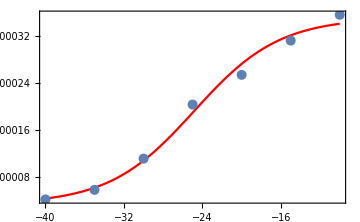

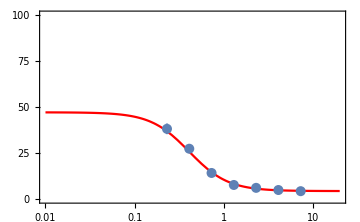

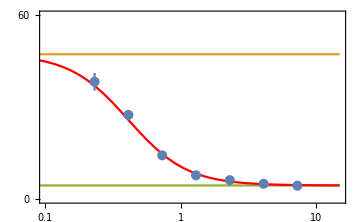

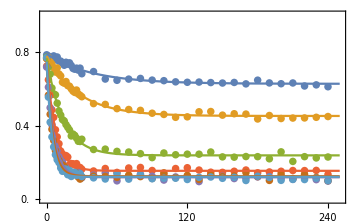

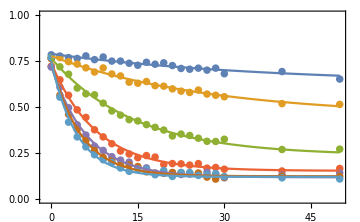

```mathematica
T1guess=60.93060222779;
G10guess=1/(2*Pi*T1guess);
initguessS={{G10,G10guess},{G21,0.0000274436},{a,0.00120406}};
initguessS={{G10,G10guess},{G21,0.0000188207},{a,aEstimate}};
BoundS={1/(2*Pi*40.*10^3)>G10>1/(2.*Pi*200*10^3),0.0000374436>G21>0.00001764436,aEstimate*1.2>a>aEstimate*0.8};
(*BoundS={G10<1/(2*Pi*4*10^4),G10>1/(2*Pi*80*10^4),G21<0.0000374436,G21>0.00001764436,a<0.00220406,a>0.00020406};*)
model=G10+(G21*(a*10^(p/10))/((G20+G21)^2+2*(a*10^(p/10))));
(*Gfit2=FindFit[Transpose[{power,Gpump}],{G10+(G21*(a*10^(p/10))/((G20+G21)^2+2*(a*10^(p/10))))
,BoundS},{{G10, G10guess},{G21,0.0005}, {a,0.002}},p,AccuracyGoal->50]*)
(*nmf=NonlinearModelFit[Transpose[{power,Gpump}],{model},initguessS,p, Method->{NMinimize,Method->{"DifferentialEvolution","PostProcess"->{FindMinimum,Method->"QuasiNewton"}}}];*)
nmf=NonlinearModelFit[Transpose[{power,Gpump}],{model},initguessS,p];
(*Gfit2={G10->initguessS[[1,2]],G21->initguessS[[2,2]],a->initguessS[[3,2]]}*)
Gfit2=nmf["BestFitParameters"]
nmf["ParameterConfidenceIntervalTable"]
BoundS
initguessS
G10fix=G10/.Gfit2;
T1fix=1/(2π G10fix)
1/(2π G21)/.Gfit2
10^-3/(π G21)/.Gfit2
"branching ratio "<>ToString[G20/G21/.Gfit2]
Show[Plot[(G10+(G21*(a*10^(p/10))/((G20+G21)^2+2*(a*10^(p/10)))))/.Gfit2,{p,Min[power],Max[power]}, PlotRange->All,PlotStyle->Red],
ListPlot[Transpose[{power,Gpump}],PlotStyle->PointSize[0.02]]
,Frame->True,ImageSize->Medium,FrameTicksStyle->Directive[Black,16]]

Omega=Sqrt[a*10^(power/10)]/.Gfit2;
toplotT=Table[{{10^3 Omega[[i]],10^-3 Tpump[[i]]},ErrorBar[10^-3 σTpump[[i]]]},{i,1,Length@power}];

branching=Show[LogLinearPlot[10^-3/(2*Pi*(G10+(G21*(Ω*10^-3)^2/((G20+G21)^2+2*(Ω*10^-3)^2))))/.Gfit2,{Ω,0.01,20}, PlotRange->{0,100},PlotStyle->Red],
ErrorListLogLinearPlot[toplotT,PlotStyle->PointSize[0.02]]
,Frame->True,ImageSize->Medium,FrameTicksStyle->Directive[Black,16]]

branching=Show[LogLinearPlot[{10^-3 T1fix,10^-3 T1fix,10^-3/(π G21+2π G10fix)/.Gfit2},{x,0.01,15}, FrameTicks->{{Table[0+30i,{i,0,5}],None},{{0.1, 0.32,1,3.2,10},None}},PlotStyle->{None,Automatic,Automatic}],LogLinearPlot[10^-3/(2*Pi*(G10+(G21*(Ω*10^-3)^2/((G20+G21)^2+2*(Ω*10^-3)^2))))/.Gfit2,{Ω,0.01,15}, PlotRange->All,PlotStyle->Red],
ErrorListLogLinearPlot[toplotT,PlotStyle->PointSize[0.02]],PlotRange->{{Log[0.1],Log[15]},{0,60}}
,Frame->True,ImageSize->Medium,FrameTicksStyle->Directive[Black,16]]
g=Show[ListPlot[Table[Transpose[{10^-3 delays[[loopi]],population[[loopi]]}],{loopi,1,numberloop}],PlotRange->{{-1,250},{0,1}},PlotStyle->PointSize[0.015]],
Plot[Evaluate@Table[Amp[[i]]Exp[-1000t/Tpump[[i]]]+Bs[[i]],{i,1,Length@Tpump}],{t,0,250}],Frame->True,FrameTicks->{{Table[0.2i,{i,0,5}],None},{Table[40i,{i,0,10}],None}}, FrameTicksStyle->Directive[Black,16],ImageSize->Medium]

Show[ListPlot[Table[Transpose[{10^-3 delays[[loopi]],population[[loopi]]}],{loopi,1,numberloop}],PlotRange->{{-1,50},{0,1}},PlotStyle->PointSize[0.015]],
Plot[Evaluate@Table[Amp[[i]]Exp[-1000t/Tpump[[i]]]+Bs[[i]],{i,1,Length@Tpump}],{t,0,50}],Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium]
```

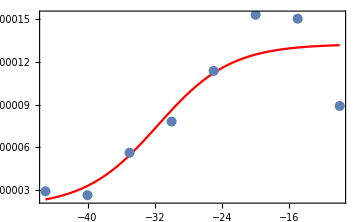

-Graphics-

```mathematica
Export[path<>"branching.eps",branching]
Export[path<>"branching.png",branching]
Export[path<>"transient.eps",g]
Export[path<>"transient.png",g]
```

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\branching.eps

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\branching.png

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\transient.eps

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\transient.png

```mathematica
Simplify[(10^3 2*Pi)^2*a*10^3/.Gfit2]/.p->-60
```

9.827×10^7

{G21→0.0000263436,a→0.00103117}

| Estimate | Standard Error | Confidence Interval
G21 | 0.0000263436 | 1.21087×10^-6 | {0.0000232309,0.0000294562}
a | 0.00103117 | 0.000223076 | {0.000457738,0.00160461}

branching ratio 68.5984

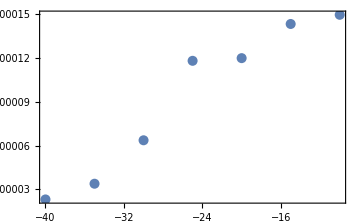

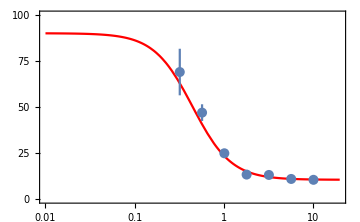

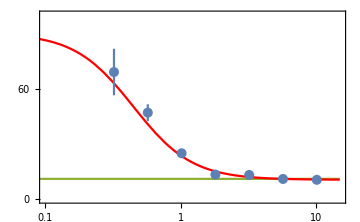

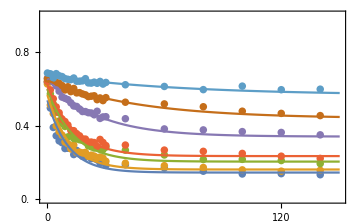

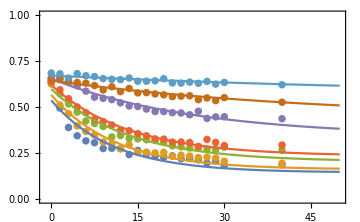

```mathematica
T1guess=90000.;
G20=0.0018071254414408456;
G10guess=1/(2*Pi*T1guess);
initguessS={{G21,0.0000274436},{a,0.00120406}};
model=G10guess+(G21*(a*10^(p/10))/((G20+G21)^2+2*(a*10^(p/10))));
(*Gfit2=FindFit[Transpose[{power,Gpump}],{G10+(G21*(a*10^(p/10))/((G20+G21)^2+2*(a*10^(p/10))))
,BoundS},{{G10, G10guess},{G21,0.0005}, {a,0.002}},p,AccuracyGoal->50]*)
nmf=NonlinearModelFit[Transpose[{power,Gpump}],{model},initguessS,p];
(*Gfit2={G10->initguessS[[1,2]],G21->initguessS[[2,2]],a->initguessS[[3,2]]}*)
Gfit2=nmf["BestFitParameters"]
nmf["ParameterConfidenceIntervalTable"]
"branching ratio "<>ToString[G20/G21/.Gfit2]
Show[Plot[(G10+(G21*(a*10^(p/10))/((G20+G21)^2+2*(a*10^(p/10)))))/.Gfit2,{p,Min[power],Max[power]}, PlotRange->All,PlotStyle->Red],
ListPlot[Transpose[{power,Gpump}],PlotStyle->PointSize[0.02]]
,Frame->True,ImageSize->Medium,FrameTicksStyle->Directive[Black,16]]

Omega=Sqrt[a*10^(power/10)]/.Gfit2;
toplotT=Table[{{10^3 Omega[[i]],10^-3 Tpump[[i]]},ErrorBar[10^-3 σTpump[[i]]]},{i,1,Length@power}];

branching=Show[LogLinearPlot[10^-3/(2*Pi*(G10guess+(G21*(Ω*10^-3)^2/((G20+G21)^2+2*(Ω*10^-3)^2))))/.Gfit2,{Ω,0.01,20}, PlotRange->{0,100},PlotStyle->Red],
ErrorListLogLinearPlot[toplotT,PlotStyle->PointSize[0.02]]
,Frame->True,ImageSize->Medium,FrameTicksStyle->Directive[Black,16]]

branching=Show[LogLinearPlot[{10^-3 T1fix,10^-3 T1fix,10^-3/(π G21+2π G10fix)/.Gfit2},{x,0.01,15}, FrameTicks->{{Table[0+30i,{i,0,5}],None},{{0.1, 0.32,1,3.2,10},None}},PlotStyle->{None,Automatic,Automatic}],LogLinearPlot[10^-3/(2*Pi*(G10guess+(G21*(Ω*10^-3)^2/((G20+G21)^2+2*(Ω*10^-3)^2))))/.Gfit2,{Ω,0.01,15}, PlotRange->All,PlotStyle->Red],
ErrorListLogLinearPlot[toplotT,PlotStyle->PointSize[0.02]],PlotRange->{{Log[0.1],Log[15]},{0,100}}
,Frame->True,ImageSize->Medium,FrameTicksStyle->Directive[Black,16]]
g=Show[ListPlot[Table[Transpose[{10^-3 delays[[loopi]],population[[loopi]]}],{loopi,1,numberloop}],PlotRange->{{-1,150},{0,1}},PlotStyle->PointSize[0.015]],
Plot[Evaluate@Table[Amp[[i]]Exp[-1000t/Tpump[[i]]]+Bs[[i]],{i,1,Length@Tpump}],{t,0,150}],Frame->True,FrameTicks->{{Table[0.2i,{i,0,5}],None},{Table[40i,{i,0,10}],None}}, FrameTicksStyle->Directive[Black,16],ImageSize->Medium]

Show[ListPlot[Table[Transpose[{10^-3 delays[[loopi]],population[[loopi]]}],{loopi,1,numberloop}],PlotRange->{{-1,50},{0,1}},PlotStyle->PointSize[0.015]],
Plot[Evaluate@Table[Amp[[i]]Exp[-1000t/Tpump[[i]]]+Bs[[i]],{i,1,Length@Tpump}],{t,0,50}],Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium]
```

```mathematica
10^(-1/20)*1.4
```

1.24775

```mathematica
1.7/Sqrt[2]
```

1.20208

# Sup

## RB

```mathematica
PtSize
```

0.035

```mathematica
file=path<>"RB.hdf5";
data=Import[file, "Data"];
cliffords = data["/cliffords"];
y=data["/y"];
yerr=data["/yerr"];
yfit=data["/yfit"];
```

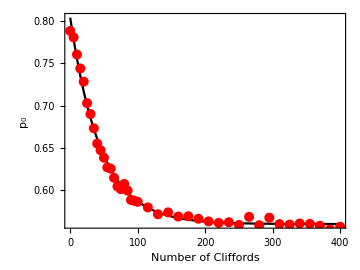

```mathematica
PtSize=0.02;
g=Show[ListPlot[Transpose@{cliffords,yfit}, PlotStyle->{PointSize[PtSize],RGBColor[0,0,0]},Joined->True],ListPlot[Transpose@{cliffords,y}, PlotStyle->{PointSize[PtSize],RGBColor[1,0,0]}], Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75,FrameLabel->{Style["Number of Cliffords",Black,18,FontFamily->"Times New Roman"],Style["p_0",Black,18,FontFamily->"Times New Roman"]}]
```

```mathematica
Export[path<>"RB.pdf",g]
```

C:\SC Lab\GitHubRepositories\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\RB.pdf

## Spectrum

```mathematica
PtSize
```

0.035

```mathematica
file=path<>"spectrum.hdf5";
data=Import[file, "Data"];
PhiExt = data["/phi_ext"];
Freq=data["/freq"];
PhiExt01=data["/phi_ext_01"];
Freqs01=data["/freqs_01"];
PhiExt02=data["/phi_ext_02"];
Freqs02=data["/freqs_02"];
PhiExt03=data["/phi_ext_03"];
Freqs03=data["/freqs_03"];
LevelsToPlot=Table[Transpose@{PhiExt,Freq[[;;,i]]},{i,1,3}];
Freqs01ToPlot=Transpose@{PhiExt01[[;;;;4]],Freqs01[[;;;;4]]};
Freqs02ToPlot=Transpose@{PhiExt02[[;;;;4]],Freqs02[[;;;;4]]};
Freqs03ToPlot=Transpose@{PhiExt03,Freqs03};
f01=Interpolation[Transpose@{PhiExt,Freq[[;;,1]]}, InterpolationOrder->2];
```

```mathematica
f01[PhiExt]
```

{1.75751,1.66307,1.57235,1.48654,1.40701,1.33533,1.27318,1.22233,1.1845,1.16114,1.15324,1.16114,1.1845,1.22233,1.27318,1.33533,1.40701,1.48654,1.57235,1.66307,1.75751,1.85462,1.95351,2.05338,2.15355,2.2534,2.35238,2.44998,2.54575,2.63927,2.73019,2.81817,2.90292,2.9842,3.06183,3.13565,3.20557,3.27153,3.33354,3.39162,3.44585,3.49631,3.54313,3.58644,3.62636,3.66306,3.69666,3.72732,3.75517,3.78032,3.80291,3.82302,3.84077,3.85624,3.86949,3.8806,3.88962,3.89658,3.90154,3.9045,3.90549,3.9045,3.90154,3.89658,3.88962,3.8806,3.86949,3.85624,3.84077,3.82302,3.80291,3.78032,3.75517,3.72732,3.69666,3.66306,3.62636,3.58644,3.54313,3.49631,3.44585,3.39162,3.33354,3.27153,3.20557,3.13565,3.06183,2.9842,2.90292,2.81817,2.73019,2.63927,2.54575,2.44998,2.35238,2.2534}

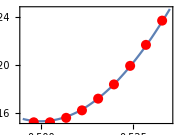

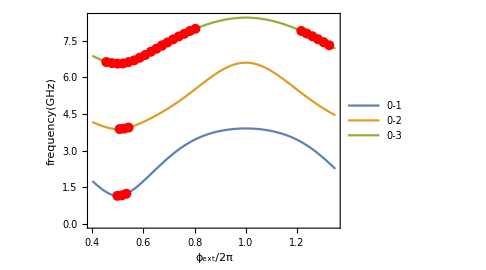

```mathematica
PtSize=0.02;

g0=Show[Plot[f01[x],{x,0.495,0.535},PlotStyle->{PointSize[0.04]},Frame->True],ListPlot[{Transpose@{PhiExt01,Freqs01}}, PlotStyle->Directive[PointSize[0.04],RGBColor[1,0,0]]], FrameTicksStyle->Directive[Black,14],ImageSize->Small,AspectRatio->0.75,Background->White,FrameTicks->Automatic]

g=Show[ListPlot[LevelsToPlot, PlotStyle->{PointSize[PtSize]},Joined->True,PlotLegends->Placed[LineLegend[{"0-1","0-2","0-3"},LegendFunction->(Framed[#]&),LabelStyle->{FontFamily->"Times New Roman",Black,14}],After]],ListPlot[{Freqs01ToPlot,Freqs02ToPlot,Freqs03ToPlot}, PlotStyle->Directive[PointSize[PtSize],RGBColor[1,0,0]]],Epilog->Inset[g0,{1.08,2.5}], Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75,FrameLabel->{Style["ϕ_ext/2π",Black,18,FontFamily->"Times New Roman"],Style["frequency(GHz)",Black,18,FontFamily->"Times New Roman"]}]
```

```mathematica
Export[path<>"spectrum.pdf",g]
```

C:\SC Lab\GitHubRepositories\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\spectrum.pdf

## 02 ramsey and rabi

```mathematica
file=path<>"02ramsey_data.hdf5";
data=Import[file, "Data"];
RamseyDelays= data["/x"];
T2Population=data["/y"];
T2Population=(1-T2Population)/0.990518111679814;
```

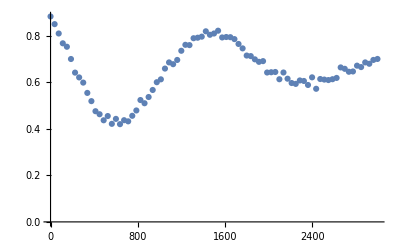

```mathematica
ListPlot[Transpose[{RamseyDelays,T2Population}]]
```

| Estimate | Standard Error | Confidence Interval
A | 0.35004 | 0.0076739 | {0.334756,0.365324}
B | 0.670358 | 0.0015904 | {0.667191,0.673526}
TR | 1.59941 | 0.0527241 | {1.4944,1.70442}
Ω | 0.568579 | 0.00273245 | {0.563137,0.574021}
ϕo | 0.833574 | 0.0157337 | {0.802238,0.864911}

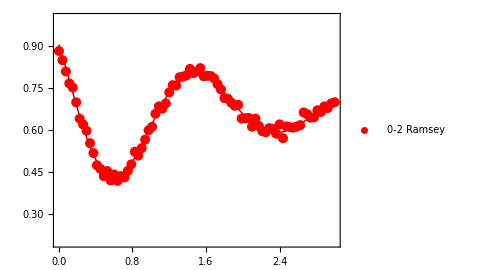

```mathematica
data=Transpose[{RamseyDelays,T2Population}];
dataRamsey=Transpose[{RamseyDelays/1000,T2Population}];
modelRamsey=A*Cos[2π*Ω*t+ϕo]*Exp[-t/TR]+B;
initguessS={{A,0.34},{B,0.69},{TR,1},{Ω,1},{ϕo,0.8}};
nmfRamsey=NonlinearModelFit[dataRamsey,modelRamsey,initguessS,t];
sparamRamsey=nmfRamsey["BestFitParameters"];
nmfRamsey["ParameterConfidenceIntervalTable"]
dataSRamsey=dataRamsey;

g1=Show[Plot[(nmfRamsey[t]/.sparamRamsey),{t,RamseyDelays[[1]]/1000,RamseyDelays[[-1]]/1000},PlotStyle->Directive[Darker@RGBColor[1,0,0],Thick],PlotRange->{0.2,1}],ListPlot[dataSRamsey,PlotStyle->Directive[RGBColor[1,0,0],PointSize[PtSize]],PlotLegends->Placed[PointLegend[{"0-2 Ramsey"},LabelStyle->{FontFamily->"Times New Roman",Black,14}],{Right,Top}]],Frame->True,FrameTicks->Automatic, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75,FrameLabel->{Style["time(μs)",Black,18,FontFamily->"Times New Roman"]}]
```

```mathematica
file=path<>"02rabi_data.hdf5";
data=Import[file, "Data"];
delays= data["/x"];
Population=data["/y"];
Population=(1-Population)/0.990518111679814;

file=path<>"01rabi_data.hdf5";
data=Import[file, "Data"];
delays01= data["/x"];
Population01=data["/y"];
Population01=(1-Population01)/1;
```

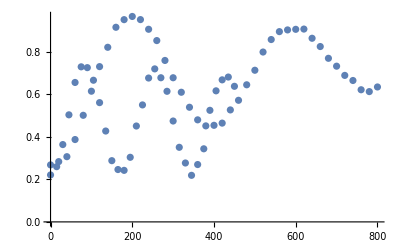

```mathematica
Show[ListPlot[Transpose[{delays,Population}]],ListPlot[Transpose[{delays01,Population01}]]]
```

```mathematica
rBot=0.999935+-0.378702-0.378759;
rTop=0.973453+-0.36176+ 0.382878
(1-rTop)/(1-rBot)
```

0.994571

0.00716675

```mathematica
rTop=0.265191+0.474671;
rBot=-0.265191+0.474671;
rBot/rTop
```

0.283134

```mathematica
1/(0.007166750712186654+0.28313388172388904 +1)
```

0.775013

```mathematica
data=Transpose[{delays/1000,Population}];
model=A*Cos[2π*Ω*t]*Exp[-t/TR]+B1*Exp[-t/Tout]+B;
initguessS={{A,-0.42},{B,0.69},{TR,0.89},{Ω,2.5},{Tout,1.89},{B1,-0.04}};
BoundS={TR>0, Tout>0, 1>B1>-1,B<1,B+B1-A<1};
(*model=A*Cos[2π*Ω*t+ϕo]*Exp[-t/TR]+B;
initguessS={{A,0.5},{B,0.6},{TR,1},{Ω,1},{ϕo,0}};*)
nmf=NonlinearModelFit[data,{model,BoundS},initguessS,t];
sparam=nmf["BestFitParameters"];
nmf["ParameterConfidenceIntervalTable"]
dataS=data;

data01=Transpose[{delays01/1000,Population01}];
model01=A*Cos[2π*Ω*t]*Exp[-t/TR]+B;
initguessS01={{A,-0.3},{B,0.5},{TR,1},{Ω,5}};
BoundS01={TR>0,B<1};
(*model=A*Cos[2π*Ω*t+ϕo]*Exp[-t/TR]+B;
initguessS={{A,0.5},{B,0.6},{TR,1},{Ω,1},{ϕo,0}};*)
nmf01=NonlinearModelFit[data01,{model01,BoundS01},initguessS01,t];
sparam01=nmf01["BestFitParameters"];
nmf01["ParameterConfidenceIntervalTable"]
dataS01=data01;
```

FittedModel::constr: The property values {ParameterConfidenceIntervalTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
A | -0.382878 | 0.00874115 | {-0.400623,-0.365132}
B | 0.973453 | 0.256441 | {0.452849,1.49406}
TR | 0.838567 | 0.0442011 | {0.748834,0.9283}
Ω | 2.50678 | 0.00661245 | {2.49335,2.5202}
Tout | 1.54337 | 1.40739 | {-1.31377,4.40051}
B1 | -0.36176 | 0.250693 | {-0.870695,0.147175}

FittedModel::constr: The property values {ParameterConfidenceIntervalTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
A | -0.265191 | 0.00747863 | {-0.280536,-0.249846}
B | 0.474671 | 0.00276437 | {0.468999,0.480343}
TR | 2.71928 | 0.826653 | {1.02312,4.41543}
Ω | 5.81769 | 0.0103971 | {5.79635,5.83902}

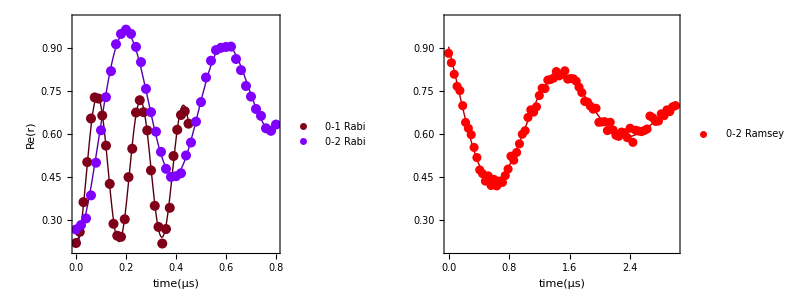

```mathematica
g1=Show[Plot[(nmfRamsey[t]/.sparamRamsey),{t,RamseyDelays[[1]]/1000,RamseyDelays[[-1]]/1000},PlotStyle->Directive[Darker@RGBColor[1,0,0],Thick],PlotRange->{0.2,1}],ListPlot[dataSRamsey,PlotStyle->Directive[RGBColor[1,0,0],PointSize[PtSize]],PlotLegends->Placed[PointLegend[{"0-2 Ramsey"},LabelStyle->{FontFamily->"Times New Roman",Black,14}],{Right,Bottom}]],Frame->True,ImageSize->327,AspectRatio->0.75,FrameTicks->True,FrameLabel->{Style["time(μs)",Black,18,FontFamily->"Times New Roman"],""},FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Directive[Black,16]},{Directive[Black,16],Directive[Black,16]}}];
g2=Show[Plot[{(nmf[t]/.sparam)},{t,delays[[1]]/1000,delays[[-1]]/1000},PlotStyle->Directive[Darker@RGBColor[0.5,0,1],Thick],PlotRange->{0.2,1}],Plot[{(nmf01[t]/.sparam01)},{t,delays01[[1]]/1000,delays01[[-1]]/1000},PlotStyle->Directive[Darker@RGBColor[0.5,0,0.1],Thick],PlotRange->{0.2,1}],ListPlot[{dataS01,dataS},PlotStyle->{{RGBColor[0.5,0,0.1],PointSize[PtSize]},{RGBColor[0.5,0,1],PointSize[PtSize]}},PlotLegends->Placed[PointLegend[{"0-1 Rabi","0-2 Rabi"},LabelStyle->{FontFamily->"Times New Roman",Black,14}],{Right,Bottom}]],Frame->True,FrameTicks->Automatic, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75,FrameLabel->{Style["time(μs)",Black,18,FontFamily->"Times New Roman"],Style["Re(r)",Black,18,FontFamily->"Times New Roman"]}];
g=Grid[{{Graphics[Text[Style["a)",FontSize->16],{0,0}],ImageSize->{20,20}],Graphics[Text[Style["b)",FontSize->16],{1,1}],ImageSize->{20,20}]},{g2,g1}},Spacings->{-0.2,-0.2},Alignment->{{Left,Left},{Bottom,Bottom}}]
```

```mathematica
.
```

```mathematica
Export[path<>"02RabiRamsey.pdf",g]
```

C:\SC Lab\GitHubRepositories\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\02RabiRamsey.pdf